Given a node subset, S ⊆V

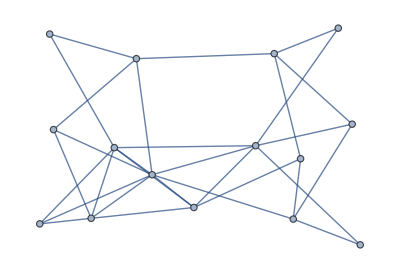
```mathematica
example=Graph[-Graphics-,VertexLabels->Automatic]
```

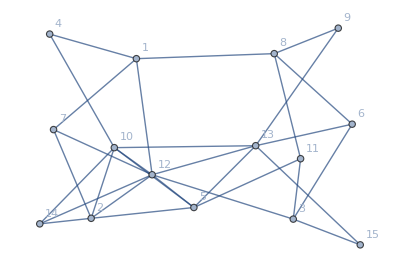

```mathematica
vertexes=VertexList[graph]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
S=RandomSample[vertexes,7]
```

{14,1,10,11,3,7,9}

```mathematica
VBackslashS=Complement[vertexes,S]
```

{2,4,5,6,8,12,13,15}

Let δ(S) denote the edge set with an end-point in S and other in V\S.

```mathematica
edges=EdgeList[graph]
```

{1<->4,1<->7,1<->8,1<->12,2<->5,2<->7,2<->10,2<->12,2<->14,3<->6,3<->11,3<->12,3<->15,4<->10,5<->10,5<->11,5<->12,5<->13,6<->8,6<->13,7<->12,8<->9,8<->11,9<->13,10<->12,10<->13,10<->14,12<->13,12<->14,13<->15}

```mathematica
MemberQ[{a,b,c},c]
```

True

```mathematica
First[1<->4]
```

1

There is a symmetry relation either 1 is in S and 4 is in V\S or 1 is in V\S and 4 is in S

```mathematica
MemberQ[S,First[1<->4]]
```

True

```mathematica
MemberQ[VBackslashS,Last[1<->4]]
```

True

1<->4 is in δ(s)

```mathematica
DeltaQ[edge_UndirectedEdge]:=(MemberQ[S,First[edge]]∧MemberQ[VBackslashS,Last[edge]])∨(MemberQ[S,Last[edge]]∧MemberQ[VBackslashS,First[edge]])
```

```mathematica
DeltaQ[1<->4]
```

True

```mathematica
Select[edges,DeltaQ]
```

{1<->4,1<->8,1<->12,2<->7,2<->10,2<->14,3<->6,3<->12,3<->15,4<->10,5<->10,5<->11,7<->12,8<->9,8<->11,9<->13,10<->12,10<->13,12<->14}

```mathematica
Delta[graph_?GraphQ,subset_]:=Block[{vertexes,edges,VBackslashS},edges=EdgeList[graph];vertexes=VertexList[graph];VBackslashS=Complement[vertexes,subset];Select[edges,((MemberQ[subset,First[#]]∧MemberQ[VBackslashS,Last[#]])∨(MemberQ[subset,Last[#]]∧MemberQ[VBackslashS,First[#]])==True)&]]
```

Check the function

```mathematica
Delta[example,{14,1,10,11,3,7,9}]
```

{1<->4,1<->8,1<->12,2<->7,2<->10,2<->14,3<->6,3<->12,3<->15,4<->10,5<->10,5<->11,7<->12,8<->9,8<->11,9<->13,10<->12,10<->13,12<->14}

```mathematica
Delta[example,{14,1,10,11,3,7,9}]==Select[edges,DeltaQ]
```

True

Its working!

```mathematica
Length[Delta[example,{14,1,10,11,3,7,9}]]
```

30

```mathematica
Length[edges]
Length[Select[edges,DeltaQ]]
```

30

19

There are 30 edges and 19 edges in δ(S) so the algorithm seems to be working.

Let E(S) be the set of edges with both end-points in S:

```mathematica
BothEndpointsQ[edge_UndirectedEdge]:=(MemberQ[S,First[edge]]∧MemberQ[S,Last[edge]])
```

```mathematica
Select[edges,BothEndpointsQ]
```

{1<->7,3<->11,10<->14}

Given two node subsets S_1, S_2⊆V, (S_1,S_2) will represent the set of edges with one end-point in S_1 and the other in S_2.

```mathematica
EndPointsInTwoSets[graph_?GraphQ,s1_{__},s2_{__}]:=Block[{vertexes,edges},edges=EdgeList[graph];vertexes=VertexList[graph];Select[edges,((MemberQ[s1,First[#]]∧MemberQ[s2,Last[#]])∨(MemberQ[s1,Last[#]]∧MemberQ[s2,First[#]])==True)&]]
```

A vertex is called even (odd) if it is incident with an even (odd) number of edges.

```mathematica
EvenVertexQ[graph_?GraphQ,vertex_]/;MemberQ[VertexList[graph],vertex]:=EvenQ[VertexDegree[graph,vertex]]
```

```mathematica
OddVertexQ[graph_?GraphQ,vertex_]:=OddQ[VertexDegree[graph,vertex]]/;MemberQ[VertexList[graph],vertex]
```

```mathematica
EvenSubsetQ[graph_?GraphQ,subset_]:=EvenQ[Length[Select[subset,OddVertexQ[graph,#]&]]]
```

```mathematica
OddSubsetQ[graph_?GraphQ,subset_]:=OddQ[Length[Select[subset,OddVertexQ[graph,#]&]]]
```

14 and 7 are odd numbered nodes. {14} has an odd number of odd numbered nodes so it should return false and it does.

```mathematica
EvenSubsetQ[example,{14,7}]
```

True

```mathematica
EvenSubsetQ[example,{14}]
```

False

```mathematica
OddSubsetQ[example,{14}]
```

True

```mathematica
OddSubsetQ[example,{14,7}]
```

False

```mathematica
ClearAll[OddVertexQ]
```

```mathematica
Count[{1,2,3},Mod[#,2]==0&]
```

0

```mathematica
ContainsAll[{1,2,3,4},{1,2}]
```

True

```mathematica
ContainsAll[{1,2,3,4},{1,5,4}]
```

False

Let x_ij be the number of times edge (i,j) is traversed from i to j in a WPP tour.

The variables x_ij can be built into a matrix X

```mathematica
Grid[XMatrix=Table[Subscript[x, i,j],{i,VertexCount[example]},{j,VertexCount[example]}]]
```

x_(1,1) | x_(1,2) | x_(1,3) | x_(1,4) | x_(1,5) | x_(1,6) | x_(1,7) | x_(1,8) | x_(1,9) | x_(1,10) | x_(1,11) | x_(1,12) | x_(1,13) | x_(1,14) | x_(1,15)
x_(2,1) | x_(2,2) | x_(2,3) | x_(2,4) | x_(2,5) | x_(2,6) | x_(2,7) | x_(2,8) | x_(2,9) | x_(2,10) | x_(2,11) | x_(2,12) | x_(2,13) | x_(2,14) | x_(2,15)
x_(3,1) | x_(3,2) | x_(3,3) | x_(3,4) | x_(3,5) | x_(3,6) | x_(3,7) | x_(3,8) | x_(3,9) | x_(3,10) | x_(3,11) | x_(3,12) | x_(3,13) | x_(3,14) | x_(3,15)
x_(4,1) | x_(4,2) | x_(4,3) | x_(4,4) | x_(4,5) | x_(4,6) | x_(4,7) | x_(4,8) | x_(4,9) | x_(4,10) | x_(4,11) | x_(4,12) | x_(4,13) | x_(4,14) | x_(4,15)
x_(5,1) | x_(5,2) | x_(5,3) | x_(5,4) | x_(5,5) | x_(5,6) | x_(5,7) | x_(5,8) | x_(5,9) | x_(5,10) | x_(5,11) | x_(5,12) | x_(5,13) | x_(5,14) | x_(5,15)
x_(6,1) | x_(6,2) | x_(6,3) | x_(6,4) | x_(6,5) | x_(6,6) | x_(6,7) | x_(6,8) | x_(6,9) | x_(6,10) | x_(6,11) | x_(6,12) | x_(6,13) | x_(6,14) | x_(6,15)
x_(7,1) | x_(7,2) | x_(7,3) | x_(7,4) | x_(7,5) | x_(7,6) | x_(7,7) | x_(7,8) | x_(7,9) | x_(7,10) | x_(7,11) | x_(7,12) | x_(7,13) | x_(7,14) | x_(7,15)
x_(8,1) | x_(8,2) | x_(8,3) | x_(8,4) | x_(8,5) | x_(8,6) | x_(8,7) | x_(8,8) | x_(8,9) | x_(8,10) | x_(8,11) | x_(8,12) | x_(8,13) | x_(8,14) | x_(8,15)
x_(9,1) | x_(9,2) | x_(9,3) | x_(9,4) | x_(9,5) | x_(9,6) | x_(9,7) | x_(9,8) | x_(9,9) | x_(9,10) | x_(9,11) | x_(9,12) | x_(9,13) | x_(9,14) | x_(9,15)
x_(10,1) | x_(10,2) | x_(10,3) | x_(10,4) | x_(10,5) | x_(10,6) | x_(10,7) | x_(10,8) | x_(10,9) | x_(10,10) | x_(10,11) | x_(10,12) | x_(10,13) | x_(10,14) | x_(10,15)
x_(11,1) | x_(11,2) | x_(11,3) | x_(11,4) | x_(11,5) | x_(11,6) | x_(11,7) | x_(11,8) | x_(11,9) | x_(11,10) | x_(11,11) | x_(11,12) | x_(11,13) | x_(11,14) | x_(11,15)
x_(12,1) | x_(12,2) | x_(12,3) | x_(12,4) | x_(12,5) | x_(12,6) | x_(12,7) | x_(12,8) | x_(12,9) | x_(12,10) | x_(12,11) | x_(12,12) | x_(12,13) | x_(12,14) | x_(12,15)
x_(13,1) | x_(13,2) | x_(13,3) | x_(13,4) | x_(13,5) | x_(13,6) | x_(13,7) | x_(13,8) | x_(13,9) | x_(13,10) | x_(13,11) | x_(13,12) | x_(13,13) | x_(13,14) | x_(13,15)
x_(14,1) | x_(14,2) | x_(14,3) | x_(14,4) | x_(14,5) | x_(14,6) | x_(14,7) | x_(14,8) | x_(14,9) | x_(14,10) | x_(14,11) | x_(14,12) | x_(14,13) | x_(14,14) | x_(14,15)
x_(15,1) | x_(15,2) | x_(15,3) | x_(15,4) | x_(15,5) | x_(15,6) | x_(15,7) | x_(15,8) | x_(15,9) | x_(15,10) | x_(15,11) | x_(15,12) | x_(15,13) | x_(15,14) | x_(15,15)

Each entry x_(i,j) will be 0 by default or higher. The range is 0, 1, 2, 3, ….

Given F⊆E, we denote by x(F)=∑_({i,j}∈F)^□ (x_ij+x_ji)

```mathematica
XOfF[graph_?GraphQ,f_List]/;SubsetQ[EdgeList[graph],f]:=Sum[Indexed[x,{i,j}]+Indexed[x,{j,i}],{x,f}]
```

Testing x(F) function:

```mathematica
RandomSample[edges,7]
```

{10<->13,5<->11,4<->10,12<->14,1<->8,10<->14,2<->12}

```mathematica
XOfF[example,{10<->13,5<->11,4<->10,12<->14,1<->8,10<->14,2<->12}]
```

(1<->8)ij+(1<->8)ji+(2<->12)ij+(2<->12)ji+(4<->10)ij+(4<->10)ji+(5<->11)ij+(5<->11)ji+(10<->13)ij+(10<->13)ji+(10<->14)ij+(10<->14)ji+(12<->14)ij+(12<->14)ji

and given (S_1,S_2), we denote by x(S_1:S_2) the sum of the variables associated with the traversal from S_1 to S_2 of the edges in (S_1,S_2),

x(S_1:S_2)=∑_(i∈S_1,j∈S_2) x_ij

```mathematica
TraversalSumOfVariablesInTwoSets[graph_?GraphQ,s1_List,s2_List]/;(SubsetQ[EdgeList[graph],s1]∧SubsetQ[EdgeList[graph],s2]):=Sum[Indexed[x,{i,j}],{x,s1}]+Sum[Indexed[x,{i,j}],{x,s2}]
```

```mathematica
TraversalSumOfVariablesInTwoSets[example,RandomSample[edges,7],RandomSample[edges,7]]
```

2 (1<->4)ij+(3<->12)ij+(3<->15)ij+2 (5<->11)ij+(5<->12)ij+2 (6<->8)ij+2 (9<->13)ij+(10<->13)ij+(10<->14)ij+(13<->15)ij

symmetric identity test

```mathematica
s1example=RandomSample[edges,7]
s2example=RandomSample[edges,7]
```

{3<->6,8<->9,3<->12,5<->13,1<->12,10<->14,2<->10}

{10<->12,3<->12,10<->13,1<->8,13<->15,4<->10,1<->12}

```mathematica
TraversalSumOfVariablesInTwoSets[example,s1example,s2example]
```

(1<->8)ij+2 (1<->12)ij+(2<->10)ij+(3<->6)ij+2 (3<->12)ij+(4<->10)ij+(5<->13)ij+(8<->9)ij+(10<->12)ij+(10<->13)ij+(10<->14)ij+(13<->15)ij

```mathematica
TraversalSumOfVariablesInTwoSets[example,s1example,s2example]+TraversalSumOfVariablesInTwoSets[example,s2example,s1example]
```

2 (1<->8)ij+4 (1<->12)ij+2 (2<->10)ij+2 (3<->6)ij+4 (3<->12)ij+2 (4<->10)ij+2 (5<->13)ij+2 (8<->9)ij+2 (10<->12)ij+2 (10<->13)ij+2 (10<->14)ij+2 (13<->15)ij

Minimize

∑_((i,j)∈E) (c_(i,j)x_ij+c_ji x_ji)

Such that

## Optimization

### Objective function

Are we minimizing or maximizing?

Minimize x+y subject to the constraints x+2y≥3, x≥0, y≥0:

```mathematica
res=LinearOptimization[x+y,{x+2y≥3,x≥0,y≥0},{x,y}]
```

{x→0,y→3/2}

Maximize 5x+y subject to the constraints x+3y≤0,x≤0, y≤0, x,≤2.5:

```mathematica
LinearOptimization[-(x+2y),{7x+3y<=11,x>=0,y>=0,x-1.2y<=1.3,y<=3},{x,y}]
```

{x→0.285714,y→3.}

Let x be a matrix variable where x_ij is 1 if Jedi i battles Sith j, and 0 otherwise. The cost function is the expected number of defeats given by ∑_(i=1) ∑_(j=1) (1-p_ij)x_ij and constructed using Inactivepaclet:ref/Inactive[Timespaclet:ref/Times]:

```mathematica
p={{0.4,0.5,0.5},{0.6,0.8,0.6},{0.7,0.9,0.6}};
```

```mathematica
defeats=Total[(1-p)*x,2];
```

Since the outer colonies are far apart, each Jedi may only be assigned to one Sith, and vice versa. Also, since x_ij is 0 or 1, then x_ij≥0:

```mathematica
constraints={Total[x] - 1== 0, Total[x,{2}] -1==0, x\[VectorGreaterEqual]0};
```

Find the appropriate Jedi to face the Sith to minimize the chances of defeat:

```mathematica
rule=LinearOptimization[defeats, constraints,x∈Matrices[Dimensions[p]]]
```

{x→{{0.,0.,1.},{0.,1.,0.},{1.,0.,0.}}}

Solve a bipartite matching problem between two sets a and b that minimizes the total weight:

```mathematica
Grid[weights=Block[{n=5},SeedRandom[123];RandomReal[1,{n,n}]]]
```

0.455719 | 0.977826 | 0.943215 | 0.962216 | 0.302348
0.466709 | 0.0616383 | 0.385645 | 0.429838 | 0.778744
0.0485906 | 0.628267 | 0.277987 | 0.0902176 | 0.876587
0.109107 | 0.265758 | 0.91861 | 0.169916 | 0.0995785
0.470198 | 0.40324 | 0.971585 | 0.314929 | 0.12578

Let x be a matrix variable, where x_ij is 1 when a_i is matched to b_j and 0 otherwise. The total weight of the matching is given by ∑_(i=1) ∑_(j=1) w_ij x_ij and constructed using Inactivepaclet:ref/Inactive[Timespaclet:ref/Times]:

```mathematica
cost=Total[weights*x,2];
```

The row and column sums of x need to be 1 and also x≥0:

```mathematica
constraints={Total[x]==1,Total[x,{2}]==1,x\[VectorGreaterEqual]0};
```

Use LinearOptimizationpaclet:ref/LinearOptimization to solve the problem:

```mathematica
{minCost, rule,minimalMatrix} = LinearOptimization[cost, constraints, x∈Matrices[Dimensions[weights]],{"PrimalMinimumValue","PrimalMinimizerRules", "PrimalMinimizer"}]
```

{1.06601,{x→{{0.,0.,0.,0.,1.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.}}},{{{0.,0.,0.,0.,1.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.}}}}

```mathematica
MatrixForm[minimalMatrix]
```

((0.
0.
0.
0.
1.) | (0.
1.
0.
0.
0.) | (0.
0.
1.
0.
0.) | (1.
0.
0.
0.
0.) | (0.
0.
0.
1.
0.))

```mathematica
MatrixForm@Round[x/.rule]
```

(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0)

The matching permutation may be extracted by converting the matrix x into a graph. Roundpaclet:ref/Round is used to truncate small values that may occur due to numerical error in some methods:

```mathematica
graph=AdjacencyGraph[Round[x/.rule]];
```

Use the adjacency graph to build a bipartite graph:

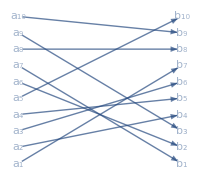

```mathematica
edges=EdgeList[graph] /. DirectedEdge[i_,j_]:> DirectedEdge[Subscript[a, i],Subscript[b, j]];
Graph[edges,]
```

### Matrix Constraints

Minimize x+y subject to the constraints x+2y==3,x≥0.5,y≥0, x∈ℤ, y∈ℝ:

```mathematica
LinearOptimization[x+y,{x+2y==3,x≥0.5,y≥0},{x∈Integers,y}]
```

{x→1,y→1.}

Use the equivalent matrix representation:

```mathematica
LinearOptimization[{1,1},{{{1,0},{0,1}},{-0.5,0}},{{{1,2}},{-3}},{Integers,Reals}]
```

{1,1.}

```mathematica
LinearOptimization[{1,1},{({{1, 0}, {0, 1}}),{-0.5,0}},{({{1, 2}}),{-3}},{Integers,Reals}]
```

{1,1.}

Minimize x+y subject to the constraints x+2y≥3 and the bounds -1≤x≤2, -1≤y≤1:

```mathematica
LinearOptimization[x+y, {x+2y≥3,-1≤x≤2,-1≤y≤1},{x,y}]
```

{x→1,y→1}

```mathematica
LinearOptimization[x+y,{x-2y,-x+y}\[VectorLessEqual]{3,2},{x,y}]
```

{x→-7,y→-5}

An equivalent form using scalar inequalities:

```mathematica
LinearOptimization[x+y,{x-2y≤3,-x+y≤2},{x,y}]
```

{x→-7,y→-5}

### Vector constraints

Minimize the function ∑_(i=1)^2 x_i+∑_(j=1)^3 y_i subject to a.x\[VectorGreaterEqual]b, y\[VectorGreaterEqual]1, y∈ℝ^3:

```mathematica
parameterEqs={a=={{1,2},{1,0}},b=={3,-1}};
```

```mathematica
parameterEqs={a==({{1, 2}, {1, 0}}),b=={3,-1}};
```

```mathematica
LinearOptimization[Total[x]+Total[y],{parameterEqs,a.x\[VectorGreaterEqual]b,y\[VectorGreaterEqual]1},{x,y}]
```

LinearOptimization::vardim: The dimensionality of variables {y} could not be determined automatically.  The dimensionality may be given by specifying variables using Element.

LinearOptimization[Total[x]+Total[y],{{a=={{1,2},{1,0}},b=={3,-1}},a.x\[VectorGreaterEqual]b,y\[VectorGreaterEqual]1},{x,y}]

Use Vectorspaclet:ref/Vectors[n] to specify the dimension of vector variables when needed:

```mathematica
LinearOptimization[Total[x]+Total[y],{parameterEqs,a.x\[VectorGreaterEqual]b,y\[VectorGreaterEqual]1},{x,y∈Vectors[3]}]
```

{x→{-1,2},y→{1,1,1}}

```mathematica
ClearAll[y]
```

```mathematica
LinearOptimization[Total[x1]+Total[y1],{parameterEqs,a.x1\[VectorGreaterEqual]b,y1\[VectorGreaterEqual]1},{x1,y1∈Vectors[3]}]
```

{x1→{-1,2},y1→{1,1,1}}

Minimize c.x subject to a.x+b\[VectorGreaterEqual]0 by directly giving the matrix a and vectors b and c:

```mathematica
{a,b,c}={c, {-3,1,1},{1,1}};
```

```mathematica
LinearOptimization[c,{a,b}]
```

{-1,2}

```mathematica
{a,b,c}={({{1, 2}, {1, 0}, {0, 1}}),{-3,1,1},{1,1}}
```

{{{1,2},{1,0},{0,1}},{-3,1,1},{1,1}}

```mathematica
LinearOptimization[c,{a,b}]
```

{-1,2}

```mathematica
AssociationMap[LinearOptimization[c,{a,b},#]&,{"PrimalMinimizer","PrimalMinimizerRules","PrimalMinimizerVector","PrimalMinimumValue","DualMaximizer","DualMaximumValue","DualityGap","Slack","ConstraintSensitivity","ObjectiveVector","LinearInequalityConstraints","LinearEqualityConstraints"}]
```

<|PrimalMinimizer→{-1,2},PrimalMinimizerRules→{x→{-1,2}},PrimalMinimizerVector→{-1,2},PrimalMinimumValue→1,DualMaximizer→{{1/2,1/2,0},{}},DualMaximumValue→1,DualityGap→0,Slack→{{0,0,3},{}},ConstraintSensitivity→{{-1/2,-1/2,0},{}},ObjectiveVector→{1,1},LinearInequalityConstraints→{SparseArray[…],{-3,1,1}},LinearEqualityConstraints→{}|>

```mathematica
MatrixForm[Thread[a.{x,y}+b≥{0,0,0}]]
```

(-3+x+2 y≥0
1+x≥0
1+y≥0)

The equivalent form using variables and inequalities:

```mathematica
constraints=Thread[a.{x,y}+b≥{0,0,0}]
```

{-3+x+2 y≥0,1+x≥0,1+y≥0}

```mathematica
LinearOptimization[c.{x,y},constraints,{x,y}]
```

{x→-1,y→2}

```mathematica
LinearOptimization[c.{x,y},constraints,{x,y}]
```

{x→-1,y→2}

```mathematica
LinearOptimization[c.z,constraints,{z∈Vectors[2]}]
```

LinearOptimization::nvcnstr: The constraint -3+x+2 y≥0 did not explicitly have any of the variables {z} and will be disregarded.

LinearOptimization[{1,1}.z,{-3+x+2 y≥0,1+x≥0,1+y≥0},{z∈Vectors[2,ℂ]}]

```mathematica
{x,x,x}
```

## Graph Optimization

```mathematica
weightedExample=Graph[example,EdgeWeight->RandomReal[4,30]]
```

-Graphics-

```mathematica
edges
```

{1<->4,1<->7,1<->8,1<->12,2<->5,2<->7,2<->10,2<->12,2<->14,3<->6,3<->11,3<->12,3<->15,4<->10,5<->10,5<->11,5<->12,5<->13,6<->8,6<->13,7<->12,8<->9,8<->11,9<->13,10<->12,10<->13,10<->14,12<->13,12<->14,13<->15}

```mathematica
AnnotationValue[weightedExample,EdgeWeight]
```

{1.46321,0.160021,3.78859,2.46084,0.365848,0.142577,0.368368,1.89197,2.00149,0.4297,2.65938,2.31685,0.30942,3.67388,0.104443,3.99293,0.168235,3.87318,0.766649,2.06677,0.927325,3.58843,1.41673,1.35988,0.34772,2.50939,1.71951,1.26107,2.05474,3.79895}

the domain will be v∈Vectors[EdgeCount[graph],Integers]

```mathematica
WeightedAdjacencyMatrix[weightedExample]
```

SparseArray[…]

```mathematica
LinearOptimization[v,{v\[VectorGreaterEqual]0},{v∈Vectors[Edge]}]
```

## Learning Linear Optimization

```mathematica
LinearOptimizationSummary[objective_,constraints_]:=AssociationMap[LinearOptimization[objective,constraints,#]&,{"PrimalMinimizer","PrimalMinimizerRules","PrimalMinimizerVector","PrimalMinimumValue","DualMaximizer","DualMaximumValue","DualityGap","Slack","ConstraintSensitivity","ObjectiveVector","LinearInequalityConstraints","LinearEqualityConstraints"}]
```

```mathematica
LinearOptimizationSummary[objective_,constraints_,variables_]:=AssociationMap[LinearOptimization[objective,constraints,variables,#]&,{"PrimalMinimizer","PrimalMinimizerRules","PrimalMinimizerVector","PrimalMinimumValue","DualMaximizer","DualMaximumValue","DualityGap","Slack","ConstraintSensitivity","ObjectiveVector","LinearInequalityConstraints","LinearEqualityConstraints"}]
```

### Basic Examples

Minimize x+y subject to the constraints x+2y≥3, x≥0, y≥0:

```mathematica
res=LinearOptimization[x+y,{x+2y≥3,x≥0,y≥0},{x,y}]
```

{x→0,y→3/2}

```mathematica
LinearOptimizationSummary[x+y,{x+2y≥3,x≥0,y≥0},{x,y}]
```

<|PrimalMinimizer→{0,3/2},PrimalMinimizerRules→{x→0,y→3/2},PrimalMinimizerVector→{0,3/2},PrimalMinimumValue→3/2,DualMaximizer→{{1/2,1/2,0},{}},DualMaximumValue→3/2,DualityGap→0,Slack→{{0,0,3/2},{}},ConstraintSensitivity→{{-1/2,-1/2,0},{}},ObjectiveVector→{1,1},LinearInequalityConstraints→{SparseArray[…],{-3,0,0}},LinearEqualityConstraints→{}|>

```mathematica
LinearOptimization[x+y,{x+2y≥3,x≥0,y≥0},{x,y},"LinearInequalityConstraints"]
```

{SparseArray[…],{-3,0,0}}

```mathematica
First[LinearOptimization[x+y,{x+2y≥3,x≥0,y≥0},{x,y},"LinearInequalityConstraints"]]
```

SparseArray[…]

```mathematica
MatrixForm[First[LinearOptimization[x+y,{x+2y≥3,x≥0,y≥0},{x,y},"LinearInequalityConstraints"]]]
```

(1 | 2
1 | 0
0 | 1)

## Simple Example

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

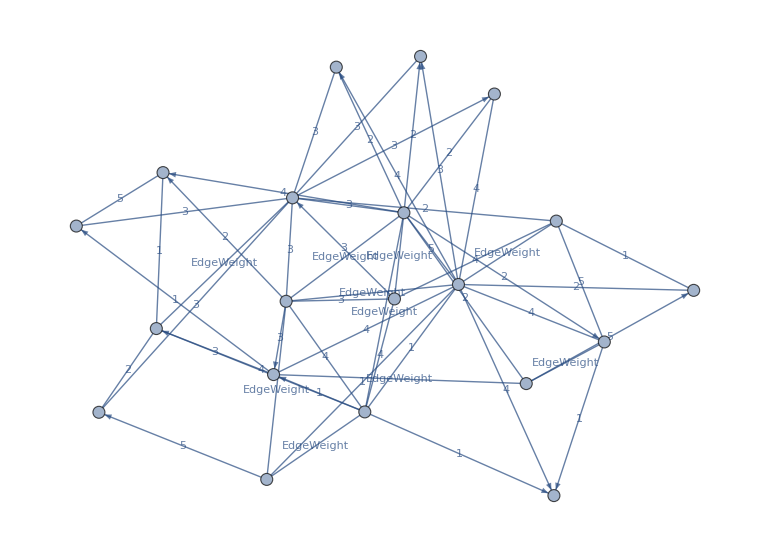

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[20,3],0.5,RandomInteger[{1,5}]&,EdgeLabels->"EdgeWeight"]
```

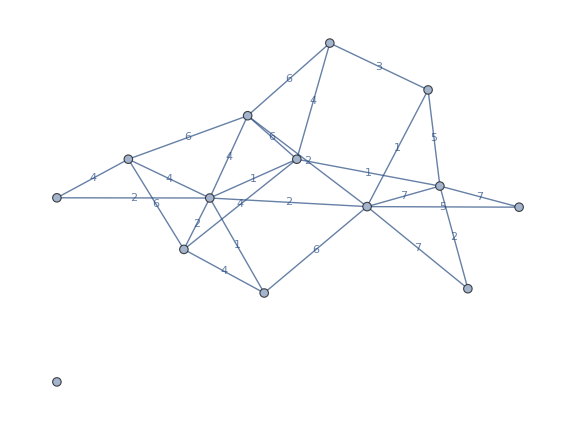

```mathematica
RandomGraph[{14,26},EdgeWeight->RandomInteger[{1,7},26],EdgeLabels->"EdgeWeight",ImageSize->Large]
```